# XX: OP Counts

We have looked at lots of algorithms.  We need a way to compare how much arithmetic they do.
Historically folks have used FLOPS (Floating Point Operations per Second) to estimate the arithmetic intensity of algorithms.  There is more than a little bit of ambiguity and tradition in this.

Olden Days: a single addition was much faster than a single multiplication; a single multiplication was much faster than a single division; and a single division was much faster than a single square root.

±≪*≪÷≪√

Single CPU or “compute”

Counting the number of multiplications was a reasonable way to estimate how much work an algorithm was

FLOP = # of multiplications

Then: a single addition was a bit faster than a single multiplication; a single multiplication was faster than a single division; and a single division was much faster than a single square root. Floating point co-processors could do a few (commonly 3 but sometimes more or less) floating point additions or multiplications at the same time

±<*<÷≪√

Single CPU with a floating point co-processor

Counting the number of multiplications was still a reasonable way to estimate algorithmic work but it was important to make sure the CPU could exploit the co-processor.

FLOP = # of multiplications

Then: a single addition was a bit faster than a single multiplication; a single multiplication was faster than a single division; and a single division was  faster than a single square root. Floating point co-processors could do a few (commonly 3 but sometimes more or less) floating point additions or multiplications at the same time

±<*<÷<√

Cheap multiple core CPUs with floating point co-processors.

A new level of communication.

Arithmetic gets cheaper much faster than memory.

Automated multi-level caches

Counting the number of “linear algebraic” operations is a reasonable way estimate algorithmic work.

Almost all of our algorithms involve mostly d⟵a*b+c

This involves reading three things, doing one multiplication, doing one addition and writing the result somewhere

FLOP = (3 memory reads, one addition, one multiplication, and one memory write)

Clusters of such CPUs

It becomes important to work out how to communicate and distribute work.

Now: A fused multiply add a*b+c (abbreviated FMAD) is slightly faster than a single division; a single division is slightly faster than a single square root. GPUs and other similar hardware can do a lot (large multiples of 32) of organized floating point arithmetic at the same time.

FMAD<÷<√

Cheap multiple core CPUs with GPUs.

Yet another new level of communication.

Arithmetic gets much cheaper and faster than memory.

More cache levels

Counting the number of “linear algebraic” operations is a reasonable way estimate algorithmic work.

Almost all of our algorithms involve mostly d⟵a*b+c

This involves reading three things, doing one multiplication, doing one addition and writing the result somewhere

FLOP = # FMADs

Clusters of such CPUs

It is still important to work out how to communicate and distribute work.

## FLOPS

### C=A.B (text book algorithm)

Assume that A is m×n_1 and B is n_1*n_2 how many FLOPS in our standard algorithm? 
	C_(i,j)=Sum[A_(i,k)B_(k,j),{j,1,n_1}]
Well the inner loop in the sum is n_2 FLOPS and we have to do it for i in 1:m and every j in 1:n_2.

The standard algorithm takes m*n_1*n_2 FMADs or modern FLOPs.

### C=A.B (Strassen and fancy Strassen-like algorithms)

Assume that m=2^n and A is m×m and B is m*m.  There is a recursive algorithm that uses fewer multiplications
than the text book algorithm.  Partition A and B and C into four equally sized parts
	(C_11 | C_12
C_21 | C_22)=C=A.B=(A_11 | A_12
A_21 | A_22).(B_11 | B_12
B_21 | B_22)
In this partitioned form the textbook algorithm is
	C_12 | = | A_11.B_11 | + | A_12.B_21
C_12 | = | A_11.B_12 | + | A_12.B_22
C_21 | = | A_21.B_11 | + | A_22.B_21
C_22 | = | A_21.B_12 | + | A_22.B_22
Of course, this has the same flop count as above! However, if
	S_1 | = | (A_11+A_22).(B_11+B_22)
S_2 | = | (A_21+A_22).B_11
S_3 | = | A_11.(B_12-B_22)
S_4 | = | A_22.(B_21-B_11)
S_5 | = | (A_11+A_12).B_22
S_6 | = | (A_21+A_11).(B_11+B_12)
S_7 | = | (A_12-A_22).(B_21+B_22)
then 
	C_11 | = | S_1+S_4-S_5+S_7
C_12 | = | S_3+S_5
C_21 | = | S_2+S_4
C_22 | = | S_1-S_2+S_3+S_6
 It is easy to check this by plugging in it is a lot harder to see how Strassen worked it out! It is also easy to implement and test it on random matrices!

#### Strassen Test

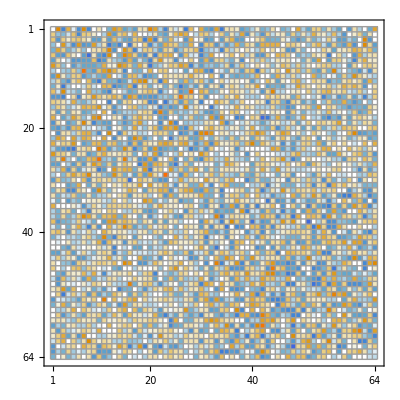

```mathematica
n=6;
m=2^n;
{A,B}=RandomReal[{-1,1},{2,m,m}];
CTextBook=A.B;
({{A11, A12}, {A21, A22}})=Partition[A,{2^(n-1),2^(n-1)}];
({{B11, B12}, {B21, B22}})=Partition[B,{2^(n-1),2^(n-1)}];
S1=(A11+A22).(B11+B22);
S2=(A21+A22).B11;
S3=A11.(B12-B22);
S4=A22.(B21-B11);
S5=(A11+A12).B22;
S6=(A21-A11).(B11+B12);
S7=(A12-A22).(B21+B22);
CStrassen=ArrayFlatten[({{S1+S4-S5+S7, S3+S5}, {S2+S4, S1-S2+S3+S6}})];
MatrixPlot[CTextBook-CStrassen,PlotLegends->Automatic]
```

```mathematica
Norm[CTextBook-CStrassen]
```

2.1569×10^-14

#### Strassen Complexity

Through some magic Strassen managed to do the big 2^n×2^n matrix multiplication using 7 small 2^(n-1)×2^(n-1) matrix matrix multiplications and 18 matrix-matrix additions rather than the 8 multiplications and 4 additions in the partitioned textbook algorithm!  The Strassen algorithm does the computation with more additions and fewer multiplications. The only way this is a good deal is if we are on computer with very fast addition and slower multiplication.

If we ignore the additions and write s(n) for the number of multiplications in the Strassen algorithm for multiplying 2^n×2^n matrices we see that we have worked out that
	s(n)=7*s(n-1)
All we need now is a base case! The algorithm takes 7 multiplications for a 2^1×2^1. In other words, s(1)=7. The solution of this recursive equation is simply s[n]=7^n. Since m=2^n we have n=ln_2(m) and we find out that Strassen’s algorithm involves
	7^(ln_2(m))=m^(Log[7]/Log[2])≈m^2.80735
multiplications! There are more complicated versions with lower exponents! A wiki page with a hopefully updating graph of the current record is at https://en.wikipedia.org/wiki/Computational_complexity_of_matrix_multiplication.
The current record seems to be 2.3728596.  There is a conjecture that there are algorithms with exponent 2+ϵ for any ϵ>0.

## FLOPS in Algorithms

### Useful Facts

∑_(i=1)^m i=1/2 m(m+1)=1/2 m^2+O(m)
∑_(i=1)^m i^2=1/6 m(m+1)(1+2m)=1/6 m^3+O(m^2)

```mathematica
Clear[m]
Sum[i,{i,1,m}]
Sum[i^2,{i,1,m}]
```

1/2 m (1+m)

1/6 m (1+m) (1+2 m)

### Gram Schmidt: Algorithm 7.1

Assume that A is m×n and look at the algorithm on p51

for j in 1:n
	v_j=a_j
	for i in 1:j-1
		r_ij=<q_i,v_j>
		v_j=v_j-r_ij q_i
	end
	r_jj=||v_j(||)_2
	q_j=v_j/r_(j,j)
end

Lets count the FMADs.

### Cholesky: Algorithm 23.1

Assume that A is m×m and SPD and look at the algorithm on p51

R= copy(A)
for k in 1:m
	for j in (k+1):m
		R[j,j:m] = R[j,j:m] - R[k,j:m]*R̄[k,j]/R[k,k]
	end
	R[k,k:m] = R[k,k:m]/√R[k,k]
end

Lets count the FMADs.